# Finite Difference Methods

## Fully Explicit Method

Forward-Difference method with expanding grid using an expansion in x space for a potential step to the limiting current region for the reaction O+e⇌R.

Version 1.30
copyright © 2002-Year Michael Honeychurch

## Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"],Clear["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
SetOptions[ListPlot3D,
AspectRatio-> 1,
AxesLabel->{
Style["k",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["j",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["c  ",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Plain,FontWeight-> Bold]},
ImageSize->288,
ViewPoint->{2,-.5,1},
Mesh->False];
```

```mathematica
SetOptions[ListPlot,
Frame->True,
FrameStyle->AbsoluteThickness[1],
GridLines->None,
ImageSize->400,
PlotStyle->{Blue,AbsoluteThickness[1]},
Joined->True];
```

```mathematica
optionA={
Axes-> False,
Frame-> True,
FrameLabel-> {
Style["k",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["z  ",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
None,
None},
FormatType-> TraditionalForm,
Frame-> False,
Joined-> False,
PlotRegion-> {{0,1},{0.1,0.9}},
PlotLabel-> None,
PlotStyle-> Thickness[0],
Prolog-> {Green,AbsolutePointSize[4.5]}
};
```

```mathematica
optionB={
Axes-> False,
Frame-> True,
FrameLabel-> {
Style["k",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["z  ",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
None,
None},
FormatType-> TraditionalForm,
Frame-> False,
Joined-> True,
PlotRegion-> {{0,1},{0.1,0.9}},
PlotLabel-> None,
PlotStyle-> {Red,Thickness[0.002]}};
```

```mathematica
$Line=0;
```

## Make Grid

```mathematica
Clear[makeGrid,n,m,c];
makeGrid[m_Integer,n_Integer]:=
	Module[{j,k},
		Clear[c];
		c=Table[1.,{m},{n}];
		For[j=1,j≤m,j++,c⟦j,1⟧=1.](*initial condition*);
		For[k=2,k≤n,k++,
				c⟦1,k⟧=0.(*boundary condition*);
				c⟦m,k⟧=1.;(*boundary condition*)
];c]
```

```mathematica
makeGrid[5,5]//MatrixForm
```

(1. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1.)

## Set Up Solution

### Procedural solution

```mathematica
Clear[explicitSolve,n,m];

explicitSolve[m_Integer,n_Integer,d_][a_]:=
	Module[{j,k,c},
c =makeGrid[m,n];
		For[k=2,k≤n,k++,
			For[j=2,j≤m-1,j++,
				c⟦j,k⟧=c⟦j-1,k-1⟧*d*a^(4-2*j)+(1-(1+a)*d*a^(3-2*j))*c⟦j,k-1⟧+c⟦j+1,k-1⟧*d*a^(3-2*j)
]
];
c];
```

### Functional solution

```mathematica
Clear[explicitSolve2];

explicitSolve2[m_Integer,n_Integer, d_][a_]:=Module[{solveNext,p},
solveNext:=Flatten[{0.,
With[{kernel=Unevaluated[{d*a^(4-2*p),(1-(1+a)*d*a^(3-2*p)),d*a^(3-2*p++)}]},
p=2;
ListCorrelate[kernel,#]
],1.}]&;
NestList[solveNext,ConstantArray[1.,{m}],n]]
```

## Set Parameter Values

```mathematica
Clear[n,a,𝔻,m];

n=100;
a=1.2;
𝔻=0.4;(*=𝔻*2/(1+a)*)
m=1+Ceiling[6*√((𝔻/a)*(n-1))];
```

## Solve it

```mathematica
Clear[c];

Timing[
c=explicitSolve[m,n,𝔻][a];
c=Transpose[c];]
```

{0.1663,Null}

```mathematica
Clear[c];

Timing[
c=explicitSolve2[m,n,𝔻][a];
c=Rest[c];]
```

{0.122753,Null}

## Plot Current v. Time

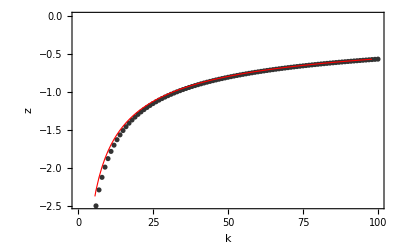

```mathematica
Clear[i,z];

i=Map[((-(#⟦2⟧*(1+a)^2)+#⟦3⟧)*√((𝔻*(n-1))/((1+a)*2*a^2)))&,c];

z=Table[-1/Sqrt[Pi*(k-1)/(n-1)],{k,2,n-1}]//N;

Show[ListPlot[i,optionA],ListPlot[z,optionB]]
```